## Load Data

```mathematica
SetDirectory[NotebookDirectory[]]
dataRaw=Import["PolicyBrief-SelectedTools.csv"];
head=dataRaw[[1]]
data=dataRaw[[2;;All]];
species=data[[All,2]]//DeleteDuplicates
```

/Users/chipdelmal/Desktop

{Tool,Specie,EIR_100,R0_100,Density_100}

{An. Gambiae s.s.,An. Arabiensis,An. Funestus}

## EIR

```mathematica
counts=Cases[data,{interventions_,#,eir_,_,_}->{interventions,eir}]&/@species;
labelsTemp=Flatten[(counts[[All,All,1]]//Transpose)[[2;;All]]]//DeleteDuplicates;
replace=StringReplace[#,"_"->" , "]&/@labelsTemp;
replaceLast=StringPosition[#," ,"]&/@replace;
lastPositions=Last/@replaceLast;
replacedLast=StringReplacePart[#[[2]],"]: ",#[[1]]]&/@Transpose[{lastPositions,replace}];
prependFirst=StringInsert[#,"%",-1]&/@(StringInsert[#,"[",1]&/@replacedLast);
```

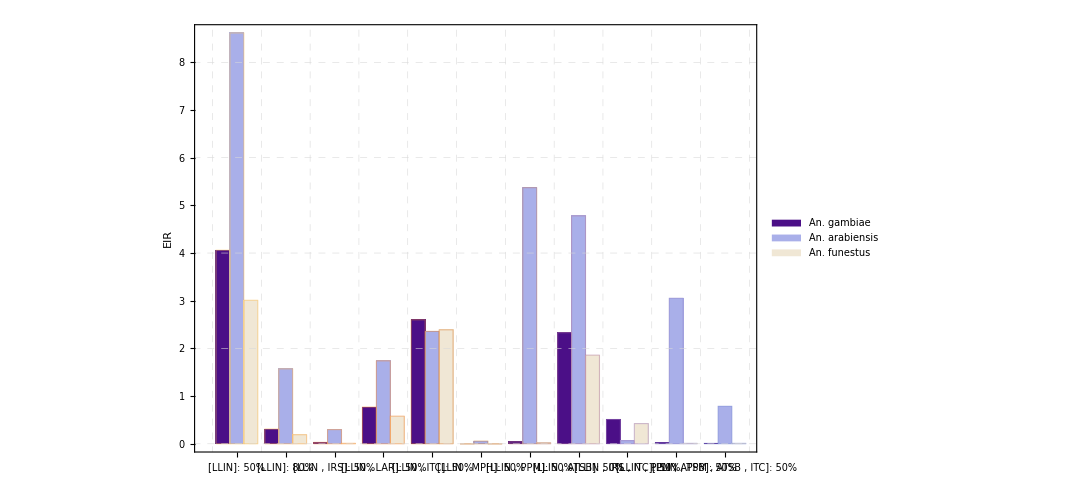

EIR_coolChart.png

```mathematica
BarChart[(counts[[All,All,2]]//Transpose)[[2;;All]],
FrameLabel->{"","EIR"},
FrameStyle->Thickness[.002],
ChartStyle->{EdgeForm[Thick],"LakeColors"},
LabelStyle->{20,20},
Frame->True,
ChartLabels->{None,Style[#,Bold,15]&/@(Rotate[#,90Degree]&/@prependFirst),None},
ChartLegends->{"An. gambiae","An. arabiensis","An. funestus"},
ImageSize->800,
GridLines->{Range[.5,100,3.5],Range[0,100,2]},
GridLinesStyle->Directive[{Dashed,Thickness[.0005]}],
BarSpacing->{0,.5}
]
Export["EIR_coolChart.png",%,ImageSize->2000,ImageResolution->200]
```

## R0

```mathematica
counts=Cases[data,{interventions_,#,_,eir_,_}->{interventions,eir}]&/@species;
labelsTemp=Flatten[(counts[[All,All,1]]//Transpose)[[2;;All]]]//DeleteDuplicates;
replace=StringReplace[#,"_"->" , "]&/@labelsTemp;
replaceLast=StringPosition[#," ,"]&/@replace;
lastPositions=Last/@replaceLast;
replacedLast=StringReplacePart[#[[2]],"]: ",#[[1]]]&/@Transpose[{lastPositions,replace}];
prependFirst=StringInsert[#,"%",-1]&/@(StringInsert[#,"[",1]&/@replacedLast);
```

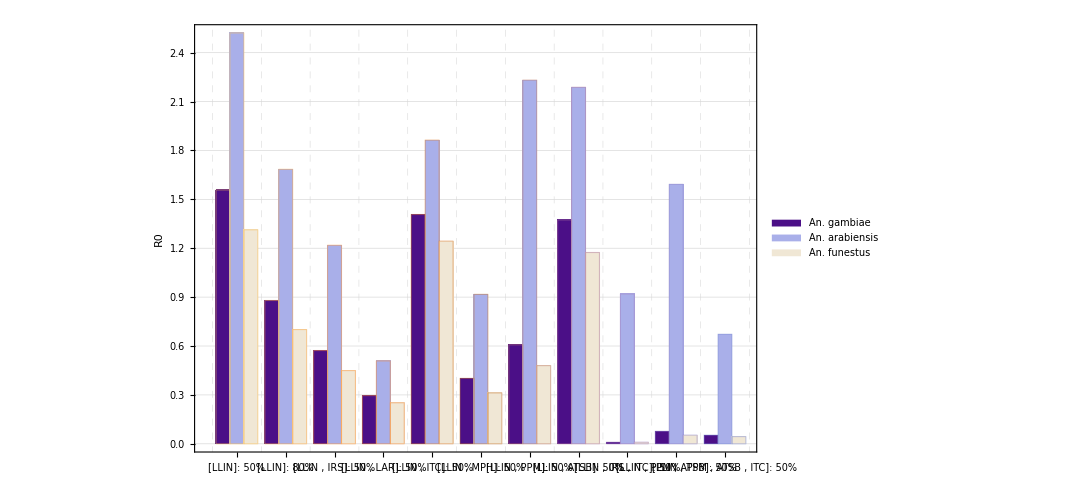

R0_coolChart.png

```mathematica
BarChart[(counts[[All,All,2]]//Transpose)[[2;;All]],
FrameLabel->{"","R0"},
FrameStyle->Thickness[.002],
ChartStyle->{EdgeForm[Thick],"LakeColors"},
LabelStyle->{20,20},
Frame->True,
ChartLabels->{None,Style[#,Bold,15]&/@(Rotate[#,90Degree]&/@prependFirst),None},
ChartLegends->{"An. gambiae","An. arabiensis","An. funestus"},
ImageSize->800,
GridLines->{Range[.5,100,3.5],Range[0,100,.5]},
GridLinesStyle->Directive[{Dashed,Thickness[.0005]}],
BarSpacing->{0,.5}
]
Export["R0_coolChart.png",%,ImageSize->2000,ImageResolution->200]
```

## Density

```mathematica
counts=Cases[data,{interventions_,#,_,_,eir_}->{interventions,eir}]&/@species;
labelsTemp=Flatten[(counts[[All,All,1]]//Transpose)[[2;;All]]]//DeleteDuplicates;
replace=StringReplace[#,"_"->" , "]&/@labelsTemp;
replaceLast=StringPosition[#," ,"]&/@replace;
lastPositions=Last/@replaceLast;
replacedLast=StringReplacePart[#[[2]],"]: ",#[[1]]]&/@Transpose[{lastPositions,replace}];
prependFirst=StringInsert[#,"%",-1]&/@(StringInsert[#,"[",1]&/@replacedLast);
```

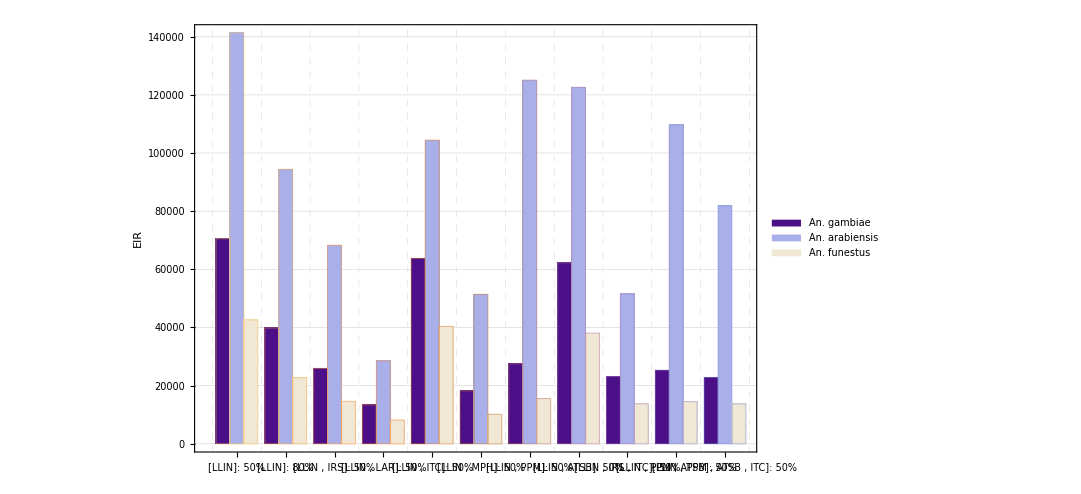

MD_coolChart.png

```mathematica
BarChart[(counts[[All,All,2]]//Transpose)[[2;;All]],
FrameLabel->{"","EIR"},
FrameStyle->Thickness[.002],
ChartStyle->{EdgeForm[Thick],"LakeColors"},
LabelStyle->{20,20},
Frame->True,
ChartLabels->{None,Style[#,Bold,15]&/@(Rotate[#,90Degree]&/@prependFirst),None},
ChartLegends->{"An. gambiae","An. arabiensis","An. funestus"},
ImageSize->800,
GridLines->{Range[.5,100,3.5],Range[0,10000000,20000]},
GridLinesStyle->Directive[{Dashed,Thickness[.0005]}],
BarSpacing->{0,.5}
]
Export["MD_coolChart.png",%,ImageSize->2000,ImageResolution->200]
```